```mathematica
1.4 Computing Actions
```

```mathematica
L[t_,x_,v_]:=1/2 m v.v-1/2 k x.x
```

```mathematica
q[t_]:={x[t],y[t],z[t]}
```

```mathematica
L@@Γ[q][t]
```

-1/2 k (x[t]^2+y[t]^2+z[t]^2)+1/2 m (x'[t]^2+y'[t]^2+z'[t]^2)

```mathematica
ⅆ/ⅆt(∂LH)/(∂q̇)-(∂LH)/(∂q)//MaTeX
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(f+g)'
```

(f+g)'

```mathematica
Subscript[δ, η] g[q]
```

```mathematica
lim_(ϵ->0) Dt[η,t,Constants->{ϵ}]/.η->η[t]
```

η'[t]

```mathematica
g[q_]:=Dt[q,{t,1},Constants->{ϵ}]
```

```mathematica
g[q+ϵ η]
```

Dt[q,t,Constants→{ϵ}]+ϵ Dt[η,t,Constants→{ϵ}]

```mathematica
Paths of minimum action
```

```mathematica
q[t_]:={4t+7,3t+5,2t+1}
```

```mathematica
Makeη[ν_,t1_,t2_][t_]:=(t-t1)(t-t2)Through[ν [t]]
```

```mathematica
SA[m_,q_,ν_,t1_,t2_][ϵ_]:=S[LFreeParticle[m],t|->q[t]+ϵ Makeη[ν,t1,t2][t],t1,t2]
```

```mathematica
SA[3.0,q,ν,0,10][0.001]
```

436.291

```mathematica
NMinimize[SA[3.0,q,ν,0,10][ϵ],ϵ]
```

{435.,{ϵ→0.}}

```mathematica
MakePath[t0_, q0_, t1_, q1_, qs_] :=
    Block[{n, ts},n = Length[qs];ts = Subdivide[t0, t1, n+1];
        Interpolation[Transpose[{ts,{q0}~Join~qs~Join~{q1}}]]
    ]
```

```mathematica
MakePath[0,0,1,1,{0.2,0.3,0.7}]
```

InterpolatingFunction[…]

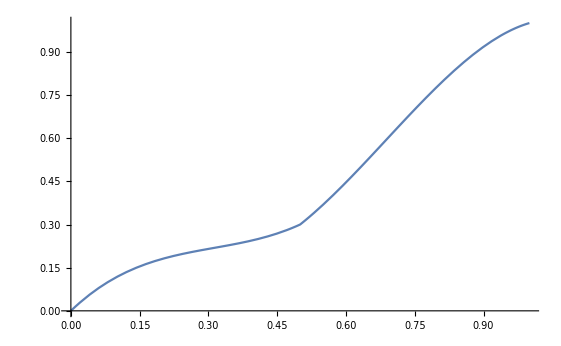

```mathematica
Plot[MakePath[0,0,1,1,{0.2,0.3,0.7}][t],{t,0,1}]
```

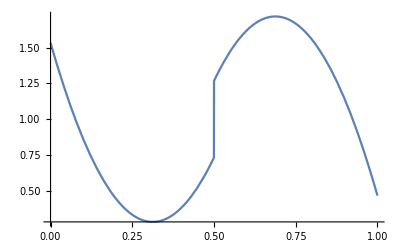

```mathematica
Plot[MakePath[0,0,1,1,{0.2,0.3,0.7}]'[t],{t,0,1}]
```

```mathematica
Finding trajectories that minimize the action
```

```mathematica
ParametricPathAction[L_,t0_,q0_,t1_,q1_][qs_]:=Module[{path},
path=MakePath[t0, q0, t1, q1, qs];
NIntegrate@@S[L,path,t0,t1] 
]
```

```mathematica
NIntegrate@@S[LFreeParticle[1],MakePath[0,0,1,1, {0.2,0.3,0.7}],0,1]
```

0.635111

```mathematica
ParametricPathAction[LFreeParticle[1],0,0,1,1][{0.2,0.3,0.7}]
```

0.635111

```mathematica
FindLPath[L_,t0_,q0_,t1_,q1_,n_]:=Block[
{vars, minimizingqs},
(*initialqs=Subdivide[q0, q1, n+1];*)
vars=Table[Symbol["$x"<>ToString@i],{i,n}];
minimizingqs=NMinimize[ParametricPathAction[L,t0,q0,t1,q1][vars],vars];
MakePath[t0,q0,t1,q1,vars/.minimizingqs⟦2⟧]
]
```

```mathematica
Clear[LHarmonic];LHarmonic[m_,k_][_,coord_,vel_]:=1/2 m Norm[vel]^2-1/2 k Norm[coord]^2
```

```mathematica
path=FindLPath[LHarmonic[1,1],0,1,π/2,0,2];
```

NIntegrate::inumr: The integrand -1/2 Norm[InterpolatingFunction[{{0,Times[«2»]}},{5,3,0,{4},{4},0,0,0,0,Automatic,«3»},{{«1»}},{{1},{$x1},{$x2},{0}},{Automatic}][t]]^2+1/2 Norm[«1»[t]]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.523599}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

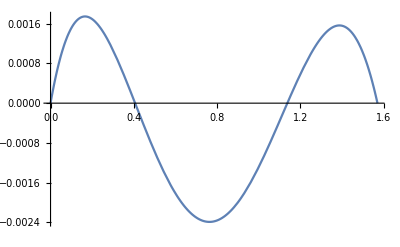

```mathematica
Plot[path[t]-Cos[t],{t,0,π/2}]
```

```mathematica
1.5 The Euler-Lagrange Equations
```

```mathematica
δ[η_][f_][q_]:=Module[{g},
g[ϵ_]:=If[Length[f]>1,Through[f[q+ϵ η]],f[q+ϵ η]];
D[g[ϵ],ϵ]/.ϵ->0
]
```

```mathematica
Clear[δ]
```

```mathematica
δ[η][f+g][Q]==δ[η][f][Q]+δ[η][g][Q]
```

```mathematica
δ[η][f g][Q]==δ[η][f][Q]g[Q]+f[Q] δ[η][g][Q]
```

True

```mathematica
Derivation of the Lagrange Equations
```

```mathematica
ClearAll[ξ,η,m,LOrbitalMotion,LHarmonic,ν]
```

```mathematica
dotrules={Times[1.,vx_]:>vx,Times[0.1,vx_]:>vx,Dot[1,vx_]:>vx, Dot[vx_,1]:>vx};
```

```mathematica
pd1[L_][args__]:=Block[{nargs=Length[List[args][[2]]]},
If[nargs>1,
Table[(Derivative[0,ReplacePart[ConstantArray[0,nargs],i->1],ConstantArray[0,nargs]][L]/.dotrules)[args],{i,1,nargs}],
(Derivative[0,1,0][L]/.dotrules)[args]
]
]
```

```mathematica
pd2[L_][args__]:=Block[{nargs=Length[List[args][[2]]]},
If[nargs>1,
Table[(Derivative[0,ConstantArray[0,nargs],ReplacePart[ConstantArray[0,nargs],i->1]][L]/.dotrules)[args],{i,1,nargs}],
(Derivative[0,0,1][L]/.dotrules)[args]
]
]
```

#### Harmonic oscillator

```mathematica
LHarmonic[t_,x_,v_]:=1/2 m v.v-1/2 k x.x
```

```mathematica
LHarmonic[t,{x,y,z},{vx,vy,vz}]
```

1/2 m (vx^2+vy^2+vz^2)-1/2 k (x^2+y^2+z^2)

```mathematica
q[t_]:={y[t]}
```

```mathematica
Γ[q][t]
```

{t,{y[t]},{y'[t]}}

```mathematica
pd1[LHarmonic]@@Γ[q][t]
```

{-k y[t]}

```mathematica
D[(pd2[LHarmonic]@@Γ[q][t]),t]-pd1[LHarmonic]@@Γ[q][t]==0//MaTeX
```

-Graphics-

#### Orbital motion

```mathematica
S[L_,q_,t1_,t2_]:=∫_t1^t2 L@*Γ[q]@tⅆt
```

```mathematica
q[t_]:={x[t],y[t]}
```

```mathematica
LOrbitalMotion[t_,x_,v_]:=1/2 m v.v+μ/(√(x.x))
```

```mathematica
LOrbitalMotion@@Γ[q][t]
```

μ/(√(x[t]^2+y[t]^2))+1/2 m (x'[t]^2+y'[t]^2)

```mathematica
D[(pd2[LOrbitalMotion]@@Γ[q][t]), t]-pd1[LOrbitalMotion]@@Γ[q][t]//MatrixForm//MaTeX
```

-Graphics-

#### Pendulum

```mathematica
LPendulum[t_,θ_,vθ_]:=1/2 m l^2 vθ.vθ+m g l Cos[θ]
```

```mathematica
q[t_]:={θ[t]}
```

```mathematica
LPendulum@@Γ[q][t]
```

{g l m Cos[θ[t]]+1/2 l^2 m θ'[t]^2}

```mathematica
D[(pd2[LPendulum]@@Γ[q][t]), t]-pd1[LPendulum]@@Γ[q][t]==0//MatrixForm//MaTeX
```

-Graphics-

#### 2d potential

```mathematica
L2dpotential[t_,r_,vr_]:=1/2 m vr.vr-V[r]
```

```mathematica
q[t_]:={x[t],y[t]}
```

```mathematica
L2dpotential@@Γ[q][t]
```

-V[{x[t],y[t]}]+1/2 m (x'[t]^2+y'[t]^2)

```mathematica
D[(pd2[L2dpotential]@@Γ[q][t]), t]-pd1[L2dpotential]@@Γ[q][t]==0//MatrixForm//MaTeX
```

-Graphics-

#### Spherical constraint

```mathematica
LSpherical[t_,r_,vr_]:=1/2 m R^2(α^2+)
```

```mathematica
q[t_]:={x[t],y[t]}
```

```mathematica
L2dpotential@@Γ[q][t]
```

-V[{x[t],y[t]}]+1/2 m (x'[t]^2+y'[t]^2)

```mathematica
D[(pd2[L2dpotential]@@Γ[q][t]), t]-pd1[L2dpotential]@@Γ[q][t]==0//MatrixForm//MaTeX
```

-Graphics-

```mathematica
Computing Lagrange's Equations
```

#### Harmonic oscillator

```mathematica
Clear[x,y,z]
```

```mathematica
LHarmonic[t_,x_,v_]:=1/2 m v.v-1/2 k x.x
```

```mathematica
LHarmonic[t,q,vq]
```

```mathematica
L(t,x,vx)=-1/2 k q.q+(m vq.vq)/2
```

```mathematica
q[t_]:={x[t]}
```

```mathematica
Γ[q][t]
```

{t,{x[t]},{x'[t]}}

```mathematica
pd1[LHarmonic]@@Γ[q][t]
```

{-k x[t]}

```mathematica
D[(pd2[LHarmonic]@@Γ[q][t]),t]-pd1[LHarmonic]@@Γ[q][t]
```

```mathematica
{k x[t]+m x''[t]}/.x->(A Cos[ω # + ϕ]&)//Simplify
```

{A (k-m ω^2) Cos[ϕ+t ω]}

#### Kepler’s third law

```mathematica
Clear[LCentralPolar]
```

```mathematica
LCentralPolar[t_,{r_,ϕ_},{vr_,vϕ_}]:=1/2 m vr.vr+1/2 m r.r vϕ.vϕ - U[r]
```

```mathematica
q[t_]:={r[t],ϕ[t]}
```

```mathematica
Γ[q][t]
```

{t,{r[t],ϕ[t]},{r'[t],ϕ'[t]}}

```mathematica
pd1[LCentralPolar]@@Γ[q][t]
```

{m ϕ'[t].ϕ'[t] r[t]-U'[r[t]],0}

```mathematica
pd2[LCentralPolar]@@Γ[q][t]
```

{m r'[t],m r[t].r[t] ϕ'[t]}

```mathematica
D[{m r'[t],m r[t].r[t] ϕ'[t]},t]
```

{m r''[t],m (r[t].r'[t]+r'[t].r[t]) ϕ'[t]+m r[t].r[t] ϕ''[t]}

```mathematica
m ϕ'[t].ϕ'[t] r[t]-U'[r[t]]/.{U->(-(G m1 m2)/#1&),m->(m1 m2)/(m1+m2)}
```

```mathematica
-(G m1 m2)/r[t]^2+(m1 m2 ϕ'[t].ϕ'[t] r[t])/(m1+m2)==0//FullSimplify
```

```mathematica
(ϕ'[t].ϕ'[t] r[t])/(m1+m2)==G/r[t]^2
```

```mathematica
How to Find Lagrangians
```

```mathematica
Constant acceleration
```

```mathematica
q[t_]:={r[t],ϕ[t]}
```

```mathematica
LConstantAccel[t_,{x_,y_},{vx_,vy_}]:=1/2 m (vx^2+vy^2)-m g y
```

```mathematica
D[(pd2[LConstantAccel]@@Γ[q][t]),t]-pd1[LConstantAccel]@@Γ[q][t]//MatrixForm//MaTeX
```

-Graphics-

```mathematica
Central force field
```

```mathematica
LConstantAccel[t_,{x_,y_},{vx_,vy_}]:=1/2 m (vx^2+vy^2)-U[√(x^2+y^2)]
```

```mathematica
D[(pd2[LConstantAccel]@@Γ[q][t]),t]-pd1[LConstantAccel]@@Γ[q][t]//MatrixForm//MaTeX
```

-Graphics-

```mathematica
D[(pd2[LConstantAccel]@@Γ[q][t]),t]-pd1[LConstantAccel]@@Γ[q][t]/.{x->(r[#]Cos[#]&),y->(r[#]Sin[#]&)}
```

```mathematica
{(Cos[t] r[t] U'[√(Cos[t]^2 r[t]^2+r[t]^2 Sin[t]^2)])/(√(Cos[t]^2 r[t]^2+r[t]^2 Sin[t]^2))+m (-Cos[t] r[t]-2 Sin[t] r'[t]+Cos[t] r''[t]),(r[t] Sin[t] U'[√(Cos[t]^2 r[t]^2+r[t]^2 Sin[t]^2)])/(√(Cos[t]^2 r[t]^2+r[t]^2 Sin[t]^2))+m (-r[t] Sin[t]+2 Cos[t] r'[t]+Sin[t] r''[t])}//FullSimplify
```

{-m Cos[t] r[t]-2 m Sin[t] r'[t]+(Cos[t] r[t] U'[√(r[t]^2)])/(√(r[t]^2))+m Cos[t] r''[t],-m r[t] Sin[t]+2 m Cos[t] r'[t]+(r[t] Sin[t] U'[√(r[t]^2)])/(√(r[t]^2))+m Sin[t] r''[t]}

```mathematica
LConstantAccelPolar[t_,{r_,p_},{vr_,vp_}]:=1/2 m (vr^2+r^2 vp^2)-U[r]
```

```mathematica
D[(pd2[LConstantAccelPolar]@@Γ[q][t]),t]-pd1[LConstantAccelPolar]@@Γ[q][t]//MatrixForm//MaTeX
```

-Graphics-

### Coordinate Transformations